0.422043

0.00032038

-0.460809

-0.000776152

0.437145

-0.0017529

-0.398365

-0.00004573

0.348888

0.00251499

-0.292266

-0.000686551

0.229329

0.119056+0.000156538 Cos[θ]-0.145335 (-1+3 Cos[θ]^2)-0.000289642 (-3 Cos[θ]+5 Cos[θ]^3)+0.0462436 (3-30 Cos[θ]^2+35 Cos[θ]^4)-0.000205002 (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)-0.0253237 (-5+105 Cos[θ]^2-315 Cos[θ]^4+231 Cos[θ]^6)-3.12264×10^-6 (-35 Cos[θ]+315 Cos[θ]^3-693 Cos[θ]^5+429 Cos[θ]^7)+0.00317027 (35-1260 Cos[θ]^2+6930 Cos[θ]^4-12012 Cos[θ]^6+6435 Cos[θ]^8)+0.0000241601 (315 Cos[θ]-4620 Cos[θ]^3+18018 Cos[θ]^5-25740 Cos[θ]^7+12155 Cos[θ]^9)-0.00147585 (-63+3465 Cos[θ]^2-30030 Cos[θ]^4+90090 Cos[θ]^6-109395 Cos[θ]^8+46189 Cos[θ]^10)-3.62821×10^-6 (-693 Cos[θ]+15015 Cos[θ]^3-90090 Cos[θ]^5+218790 Cos[θ]^7-230945 Cos[θ]^9+88179 Cos[θ]^11)+0.000315881 (231-18018 Cos[θ]^2+225225 Cos[θ]^4-1021020 Cos[θ]^6+2078505 Cos[θ]^8-1939938 Cos[θ]^10+676039 Cos[θ]^12)

-Graphics3D-

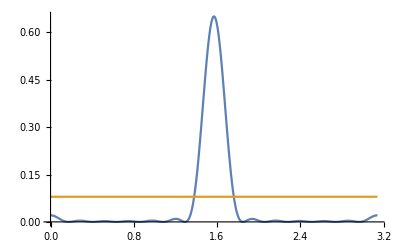

```mathematica
m1Y00=0.422043
m1Y01=0.00032038
m1Y02=-0.460809
m1Y03=-0.000776152
m1Y04=0.437145
m1Y05=-0.0017529
m1Y06=-0.398365
m1Y07=-4.573*10^-005
m1Y08=0.348888
m1Y09=0.00251499
m1Y010=-0.292266
m1Y011=-0.000686551
m1Y012=0.229329

m1[θ_]=m1Y00*SphericalHarmonicY[0,0,θ,0]+m1Y01*SphericalHarmonicY[1,0,θ,0]+m1Y02*SphericalHarmonicY[2,0,θ,0]+m1Y03*SphericalHarmonicY[3,0,θ,0]+m1Y04*SphericalHarmonicY[4,0,θ,0]+m1Y05*SphericalHarmonicY[5,0,θ,0]+m1Y06*SphericalHarmonicY[6,0,θ,0]+m1Y07*SphericalHarmonicY[7,0,θ,0]+m1Y08*SphericalHarmonicY[8,0,θ,0]+m1Y09*SphericalHarmonicY[9,0,θ,0]+
m1Y010*SphericalHarmonicY[10,0,θ,0]+m1Y011*SphericalHarmonicY[11,0,θ,0]+m1Y012*SphericalHarmonicY[12,0,θ,0]

SphericalPlot3D[{(m1[θ])^2, 1/(4 π)},{θ,0,π},{ϕ,0,π}, PlotRange -> All]
Plot[{(m1[θ])^2, 1/(4 π)},{θ,0,π}, PlotRange -> All]
```

```mathematica
N[Integrate[Sin[θ](m1[θ])^2 , {θ,0,Pi},{ϕ,0,2 Pi}]]
```

1.

```mathematica
N[Integrate[Sin[θ](m1[θ])^2 , {θ,80*π/180,100*π/180},{ϕ,0,2 Pi}]]
```

0.931529

Information::notfound: Symbol Delta not found.

```mathematica
SphericalPlot3D[{ (1/NConst)*SphericalHarmonicY[0,0,θ,ϕ]+(2/NConst)*SphericalHarmonicY[1,0,θ,ϕ] , (3/(4 Pi))^(1/3) },{θ,0,Pi},{ϕ,0,Pi}, PlotRange -> All]
```

-Graphics3D-

```mathematica
SphericalPlot3D[{ (2/NConst)*SphericalHarmonicY[1,0,θ,ϕ] , (3/(4 Pi))^(1/3) },{θ,0,Pi},{ϕ,0,Pi/2}, PlotRange -> All]
```

-Graphics3D-

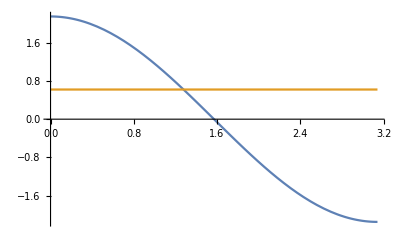

1.

```mathematica
Plot[{(2/NConst)*SphericalHarmonicY[1,0,θ,0] , (3/(4 Pi))^(1/3) },{θ,0,Pi}, PlotRange -> All]
```

```mathematica
N[m1[π/1.001]^2 * Sin[π/1.001]]
```

0.000382591